```mathematica
<<"/home/celeste/Documents/Wolfram Mathematica/second semester/448defs.m"
```

Do::iterb: Iterator {Global`lp,ν_-2,l_,-1} does not have appropriate bounds.

SetDelayed::write: Tag Times in (ⅇ^(-(Global`r)/ν_) (Global`r)^ν_)/(√(∫_0^∞ ⅇ^(-(2 Global`r)/Pattern[«2»]) (Global`r)^(2 ν_)ⅆGlobal`r))[r_] is Protected.

#### 1-2)

H=ℏ^2/(m a^2)(-1/2∂_s^2 +((l(l+1))/(2 s^2)-1/s))+(e^2 ℏ^2)/(2 m^2 c^2 a^3 s^2)L·S
((e^2 ℏ^2)/(2 m^2 c^2 a^3))/(ℏ^2/(m a^2))=1/2(e^2/(ℏ c))^2
so in atomic units
H=(-1/2∂_s^2 +((l(l+1))/(2 s^2)-1/s))+1/2 α^2/s^3 L·S
where α=e^2/ℏc=1/137
L·S=(j(j+1)-l(l+1)-s(s+1))/2=Piecewise[{{1/2, j=3/2}, {-1, j=1/2}}]

```mathematica
(A†)_l_@f_:=-D[f, r]+(1/(l+1)-(l+1)/r)f
Subscript[P, n_,l_]:=Module[{f=r^n ⅇ^(-r/n)},Do[f=(A†)_lp@f,{lp,n-2,l,-1}];f//Simplify;f/(Integrate[f^2,{r,0,∞}]^(1/2))//Simplify]
```

```mathematica
ns=Range[2,5]
```

{2,3,4,5}

```mathematica
Mso=Table[Integrate[Subscript[P, n1,1] Subscript[P, n2,1] 1/r^3,{r,0,∞}],{n1,ns},{n2,ns}]
```

{{1/24,-8/375,7/(162 √10),-1096/(50421 √5)},{-8/375,1/81,-(628 √(2/5))/50421,77/(6144 √5)},{7/(162 √10),-(628 √(2/5))/50421,1/192,-(12508 √2)/4782969},{-1096/(50421 √5),77/(6144 √5),-(12508 √2)/4782969,1/375}}

We start with j=1/2

```mathematica
H=DiagonalMatrix[-1/(2 ns^2)]-1/(2 137.^2)Mso;e1=Eigenvalues[H]
```

{-0.125001,-0.0555559,-0.0312501,-0.0200001}

Now, j = 3/2

```mathematica
H=DiagonalMatrix[-1/(2 ns^2)]+1/2 1/(2 137.^2)Mso;e2=Eigenvalues[H]
```

{-0.124999,-0.0555554,-0.0312499,-0.02}

```mathematica
e2⟦1⟧-e1⟦1⟧
```

1.66498×10^-6

This is our fine structure splitting for 2p. We compare this to  ⟨H_so⟩

```mathematica
1/2 1/137.^2 Mso⟦1,1⟧(1/2-(-1))
```

1.66498×10^-6

They are the same answer!

#### 3) Townsend 11.1

a. E^1=(b(√(ℏ/mω)))^4⟨s^4⟩=(b(√(ℏ/mω)))^4⟨((a+a^†)/(√2))^4⟩.  Only terms with equal numbers of a&a^†survive:  Using a a^†=n+1,a^†a=n

E_n^1=
     =(b(√(ℏ/mω)))^4 1/4⟨a a a^†a^†+a a^†a a^†+a a^†a^†a +a^†a^†a a+a^†a a^†a+a^†a a a^†⟩
         =b/4(ℏ/(m ω))^2(√(n+1)(n+2)√(n+1) +(n+1)(n+1)+(n+1) n+√n(n-1)√n+n n+n (n+1))

```mathematica
Simplify[(b/4)*(ℏ/(m*ω))^2*
   (Sqrt[n + 1]*(n + 2)*Sqrt[n + 1] + 
    (n + 1)*(n + 1) + (n + 1)*n + Sqrt[n]*(n - 1)*
     Sqrt[n] + n*n + n*(n + 1))]
```

(3 b (1+2 n+2 n^2) ℏ^2)/(4 m^2 ω^2)

b.  At large n, E_n^1/E_n^0=b/4(ℏ/(m ω))^2 6 n^2/(ℏ ω n)∝n so perturbation theory doesn't work at large n.

#### 4) Townsend 5

```mathematica
$Assumptions={A>0,μE>0};{eval,evec}=Eigensystem[{{μE, A}, {A, -μE}}];evec=Normalize/@evec//Simplify
```

{{(μE-√(A^2+μE^2))/(A √(2+(2 μE (μE-√(A^2+μE^2)))/A^2)),1/(√(2+(2 μE (μE-√(A^2+μE^2)))/A^2))},{(μE+√(A^2+μE^2))/(A √(2+(2 μE (μE+√(A^2+μE^2)))/A^2)),1/(√(2+(2 μE (μE+√(A^2+μE^2)))/A^2))}}

```mathematica
eval
evec0=evec/.μE->0//Simplify
```

{-√(A^2+μE^2),√(A^2+μE^2)}

{{-1/(√2),1/(√2)},{1/(√2),1/(√2)}}

We find the perturbed + state:

```mathematica
evec0⟦1⟧+evec0⟦2⟧  (evec0⟦2⟧ .{{μE, 0}, {0, -μE}}.evec0⟦1⟧)/(-2A)
```

{-1/(√2)+μE/(2 √2 A),1/(√2)+μE/(2 √2 A)}

We find the perturbed - state:

```mathematica
evec0⟦2⟧+evec0⟦1⟧  (evec0⟦1⟧ .{{μE, 0}, {0, -μE}}.evec0⟦2⟧)/(2A)
```

{1/(√2)+μE/(2 √2 A),1/(√2)-μE/(2 √2 A)}

```mathematica
Series[evec,{μE,0,1}]// Normal// PowerExpand
```

{{-1/(√2)+μE/(2 √2 A),1/(√2)+μE/(2 √2 A)},{1/(√2)+μE/(2 √2 A),1/(√2)-μE/(2 √2 A)}}

This agrees.

#### 5) Townsend 7

Start with the electric field inside the nucleus proportional to r.

E=r/R e/R^2=-∂_r ((-e r^2)/(2 R^3)+const)→ Φ=(3e)/(2R)-(e r^2)/(2 R^3)→V=(-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)

V=Piecewise[{{-e^2/r, r>R}, {(-3 e^2)/(2R)+(e^2 r^2)/(2 R^3), r<R}}]=-e^2/r+Piecewise[{{0, r>R}, {(-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)+e^2/r, r<R}}]
E^1=⟨V_1⟩=∫d^3 r ψ^2(r)((-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)+e^2/r)≈ψ^2(0)∫d^3 r ((-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)+e^2/r)
(since the s-wave wavefunction will be basically constant over the volume of the proton)

```mathematica
ψ[0]^2 Integrate[4π((-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)+e^2/r)r^2,{r,0,R}]
```

2/5 e^2 π R^2 ψ[0]^2

```mathematica
%/.ψ[0]->Limit[ (Subscript[P, 1,0][s])/(s √(Subscript[a, B]^3))1/(√(4π)),s->0]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::ivar: {{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}} is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

{{{2/5 e^2 π R^2 Limit[Indeterminate,{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2,2/5 e^2 π R^2 Limit[1/(√(ⅇ π) √(a_B^3)),{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2},{2/5 e^2 π R^2 Limit[1/(√(ⅇ π) √(a_B^3)),{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2,2/5 e^2 π R^2 Limit[Indeterminate,{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2}},{{2/5 e^2 π R^2 Limit[Indeterminate,{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2,2/5 e^2 π R^2 Limit[ⅇ^(ⅈ/2)/(√π √(a_B^3)),{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2},{2/5 e^2 π R^2 Limit[ⅇ^(-ⅈ/2)/(√π √(a_B^3)),{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2,2/5 e^2 π R^2 Limit[Indeterminate,{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2}},{{2/5 e^2 π R^2 Limit[1/(√(ⅇ π) √(a_B^3)),{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2,2/5 e^2 π R^2 Limit[Indeterminate,{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2},{2/5 e^2 π R^2 Limit[Indeterminate,{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2,2/5 e^2 π R^2 Limit[(√(ⅇ/π))/(√(a_B^3)),{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2}}}

```mathematica
%/.{e^2->14.4 eV Å, R->1.2 10^-5 Å,Subscript[a, B]->0.5292 Å}
```

General::ivar: {{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}} is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

{{{2.60576×10^-9 Å^3 eV Limit[Indeterminate,{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2,2.60576×10^-9 Å^3 eV Limit[0.88889/(√(Å^3)),{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2},{2.60576×10^-9 Å^3 eV Limit[0.88889/(√(Å^3)),{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2,2.60576×10^-9 Å^3 eV Limit[Indeterminate,{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2}},{{2.60576×10^-9 Å^3 eV Limit[Indeterminate,{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2,2.60576×10^-9 Å^3 eV Limit[(1.28613+0.702613 ⅈ)/(√(Å^3)),{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2},{2.60576×10^-9 Å^3 eV Limit[(1.28613-0.702613 ⅈ)/(√(Å^3)),{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2,2.60576×10^-9 Å^3 eV Limit[Indeterminate,{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2}},{{2.60576×10^-9 Å^3 eV Limit[0.88889/(√(Å^3)),{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2,2.60576×10^-9 Å^3 eV Limit[Indeterminate,{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2},{2.60576×10^-9 Å^3 eV Limit[Indeterminate,{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2,2.60576×10^-9 Å^3 eV Limit[2.41625/(√(Å^3)),{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}→0]^2}}}

We then decide what effect this shift has upon the Lyman α wavelength. The Lyman α radiation has slightly less energy due to the finite size of the proton. the p state wavefunction will be extremely small inside the proton, and therefore have even less of an effect:

```mathematica
Integrate[((-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)+e^2/r)(s^2/(√(24 Subscript[a, B])))^2/.s->r/Subscript[a, B],{r,0,R}]//Simplify
```

Integrate::idiv: Integral of e^2/(384 r a_B)+(e^2 r^2)/(768 R^3 a_B)-e^2/(256 R a_B) does not converge on {0,R}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

{{{0,∫_0^R (e^2 (r-R)^2 (r+2 R))/(768 r R^3 a_B)ⅆr},{∫_0^R (e^2 (r-R)^2 (r+2 R))/(768 r R^3 a_B)ⅆr,0}},{{0,∫_0^R (e^2 (r-R)^2 (r+2 R))/(768 r R^3 a_B)ⅆr},{∫_0^R (e^2 (r-R)^2 (r+2 R))/(768 r R^3 a_B)ⅆr,0}},{{∫_0^R (e^2 (r-R)^2 (r+2 R))/(768 r R^3 a_B)ⅆr,0},{0,∫_0^R (e^2 (r-R)^2 (r+2 R))/(768 r R^3 a_B)ⅆr}}}

```mathematica
%/.{e^2->14.4 eV Å, R->1.2 10^-5 Å,Subscript[a, B]->0.5292 Å}
```

Integrate::idiv: Integral of 0.-(8857.71 eV)/Å+(0.0708617 eV)/r+(2.0504×10^13 eV r^2)/Å^3 does not converge on {0,0.000012 Å}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

{{{0,∫_0^(0.000012 Å) (2.0504×10^13 eV (-0.000012 Å+r)^2 (0.000024 Å+r))/(Å^3 r)ⅆr},{∫_0^(0.000012 Å) (2.0504×10^13 eV (-0.000012 Å+r)^2 (0.000024 Å+r))/(Å^3 r)ⅆr,0}},{{0,∫_0^(0.000012 Å) (2.0504×10^13 eV (-0.000012 Å+r)^2 (0.000024 Å+r))/(Å^3 r)ⅆr},{∫_0^(0.000012 Å) (2.0504×10^13 eV (-0.000012 Å+r)^2 (0.000024 Å+r))/(Å^3 r)ⅆr,0}},{{∫_0^(0.000012 Å) (2.0504×10^13 eV (-0.000012 Å+r)^2 (0.000024 Å+r))/(Å^3 r)ⅆr,0},{0,∫_0^(0.000012 Å) (2.0504×10^13 eV (-0.000012 Å+r)^2 (0.000024 Å+r))/(Å^3 r)ⅆr}}}

#### 6) Use appropriate Clebsch-Gordan coefficients to calculate the g_j factors for a D_j^2 state.

pick a j m_j state. Use CGs to calculate ⟨L_z+2 S_z⟩=⟨J_z⟩
j=5/2 m=5/2 5/2 5/2=2 1/2→⟨L_z+2 S_z⟩=3=g_j⟨J_z⟩=g_j 5/2→ g_(5/2)=6/5 
j=3/2 m=3/2 3/2 3/2=2/(√5)2 -1/2-1/(√5)1 1/2→⟨L_z+2 S_z⟩= 4/5(1)+1/5(2)=6/5=g_j⟨J_z⟩=g_j 3/2→ g_(3/2)=4/5

```mathematica
{ClebschGordan[{2,2},{1/2,-1/2},{3/2,3/2}],ClebschGordan[{2,1},{1/2,1/2},{3/2,3/2}]}
```

{2/(√5),-1/(√5)}

#### 7) Calculate the energy levels as a function of magnetic field, and make a plotshowing both the exact results and the approximate answers from 5).

We start with the exact calculation

```mathematica
s=angmom[1/2];l=angmom[2];Hso=2/5 Sum[l⟦p⟧⊗s⟦p⟧,{p,3}];Eigenvalues[Hso]
```

{-3/5,-3/5,-3/5,-3/5,2/5,2/5,2/5,2/5,2/5,2/5}

Let a=(μ B)/E_so=B/(8.72 Gauss)

```mathematica
(12.2 MHz)/(1.3996 MHz/Gauss)
```

8.71678 Gauss

```mathematica
eD=Eigenvalues[ H=Hso+a (2 IdentityMatrix[5]⊗s⟦3⟧+l⟦3⟧⊗IdentityMatrix[2])]
```

{1/5 (2-15 a),1/5 (2+15 a),1/10 (-1-15 a-√5 √(5-6 a+5 a^2)),1/10 (-1-15 a+√5 √(5-6 a+5 a^2)),1/10 (-1-5 a-√5 √(5-2 a+5 a^2)),1/10 (-1-5 a+√5 √(5-2 a+5 a^2)),1/10 (-1+5 a-√5 √(5+2 a+5 a^2)),1/10 (-1+5 a+√5 √(5+2 a+5 a^2)),1/10 (-1+15 a-√5 √(5+6 a+5 a^2)),1/10 (-1+15 a+√5 √(5+6 a+5 a^2))}

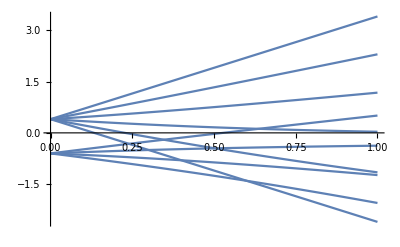

```mathematica
exactplot=Plot[Sort[eD],{a,0,1}]
```

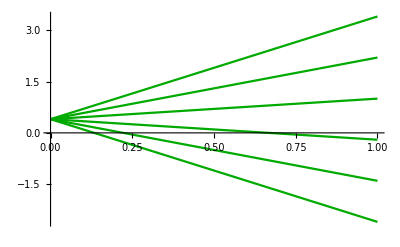

```mathematica
D52=Plot[Sort[2/5+a 6/5 Range[-5/2,5/2]],{a,0,1},PlotStyle->Darker[Green]]
```

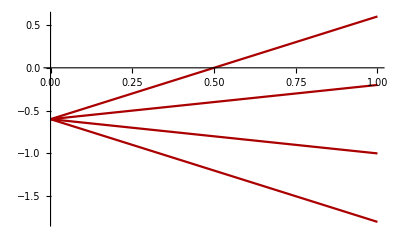

```mathematica
D32=Plot[Sort[-3/5+a 4/5 Range[-3/2,3/2]],{a,0,1},PlotStyle->Darker[Red]]
```

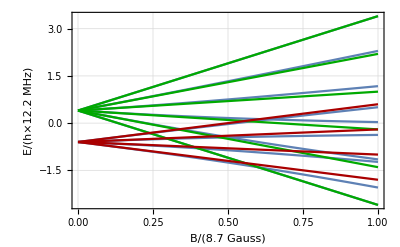

```mathematica
ThadPlot[Show[exactplot,D52,D32],{"B/(8.7 Gauss)","E/(h×12.2 MHz)"}]
```